```mathematica
casename="A";
casenumWorst=2;
casenumBest=5;
```

```mathematica
casestrWorst=casename<>"_"<>ToString[casenumWorst]<>"_.dat";
casestrBest=casename<>"_"<>ToString[casenumBest]<>"_.dat";
```

```mathematica
liftOverCamberBest=Import["/home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_sol_" <>casestrBest];
```

```mathematica
clOverCamberPrandtlBest=Import["/home/tatjam/code/tfg/workdir/steady_rectangle/prandtl_" <> casestrBest];
```

```mathematica
liftOverCamberWorst=Import["/home/tatjam/code/tfg/workdir/steady_rectangle/spanwise_sol_" <>casestrWorst];
```

#### Comparison

```mathematica
interpPrandtl=Interpolation[clOverCamberPrandtlBest[[1]]]
```

InterpolatingFunction[…]

```mathematica
interpPanelWorst=Interpolation[liftOverCamberWorst[[1]]]
```

InterpolatingFunction[…]

```mathematica
interpPanelBest=Interpolation[liftOverCamberBest[[1]]]
```

InterpolatingFunction[…]

```mathematica
resample[x_]:=x*(Length[liftOverCamberWorst[[1]]]+1)/(Length[liftOverCamberBest[[1]]]+1);
```

```mathematica
lBest=NIntegrate[(interpPanelBest[x]-interpPrandtl[x])^2,{x,1,Length[liftOverCamberBest[[1]]]}]
```

0.0177271

```mathematica
lWorst=NIntegrate[(interpPanelWorst[resample[x]]-interpPrandtl[x])^2,{x,1,Length[liftOverCamberBest[[1]]]}]
```

0.077211

InterpolatingFunction::dmval: Input value {0.762527} lies outside the range of data in the interpolating function. Extrapolation will be used.

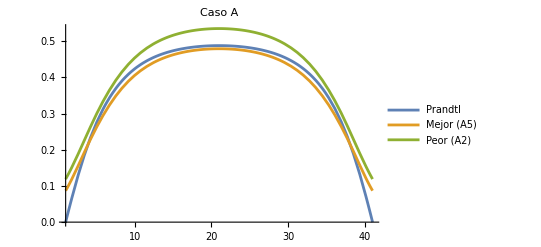

```mathematica
Plot[{interpPrandtl[x],interpPanelBest[x],interpPanelWorst[resample[x]]},
{x,1,Length[liftOverCamberBest[[1]]]},PlotLegends->{"Prandtl",
 "Mejor ("<>casename <>ToString[casenumBest]<>")", 
"Peor ("<>casename <>ToString[casenumWorst]<>")"},
	PlotLabel->"Caso "<>casename]
```